```mathematica
f[x_,y_]:=If[(x<0.5)&&(x>0),Return[{2x,y/2}],Return[{2-2x,1-y/2}]]
```

```mathematica
init=Table[{RandomReal[],0.5*RandomReal[]},5000];
init2=Table[{RandomReal[],0.5+0.5*RandomReal[]},5000];
```

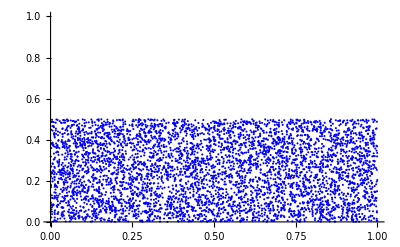

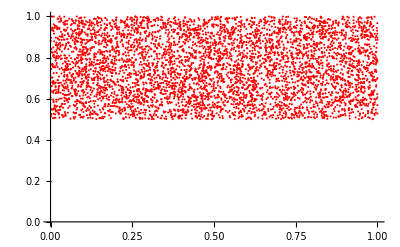

```mathematica
ListPlot[init,PlotRange->{{0,1},{0,1}},PlotStyle->Blue]
ListPlot[init2,PlotRange->{{0,1},{0,1}},PlotStyle->Red]
```

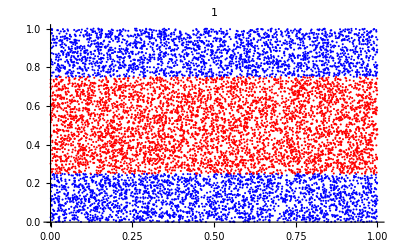
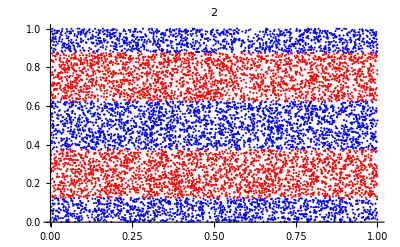
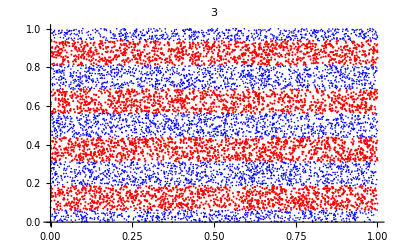
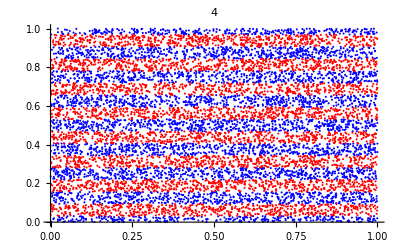
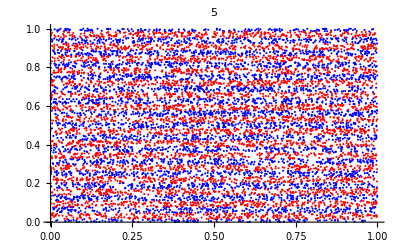
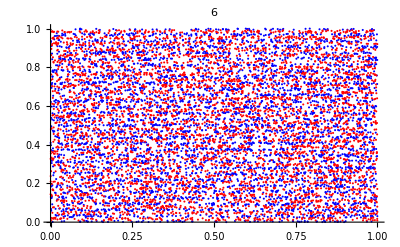
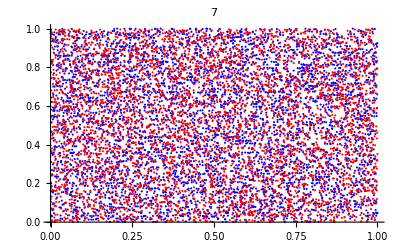
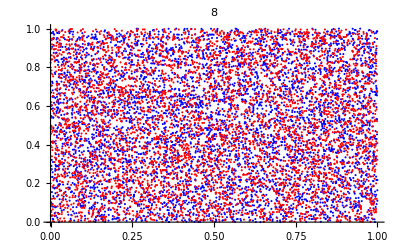

```mathematica
data=init;
data2=init2;
Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data2=Table[f[data2[[i]][[1]],data2[[i]][[2]]],{i,1,Length[init]}];
ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},{0,1}},PlotLabel->iii]~Show~ListPlot[data2,PlotStyle->Red,PlotRange->{{0,1},{0,1}}]
},{iii,1,70,1}]
```